```mathematica
prec=5;
γ=0.5//N[#,prec]&;
λ=0.5//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=J(1-γ)/2//N[#,prec]&;
a2=J (1+γ)/2//N[#,prec]&;
α[θ_]=(a0+(a2+a1) Cos[θ]);
β[θ_]=(a1-a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[α[θ],β[θ]];
```

```mathematica
Plot[{α[x],β[x],ω[x],ϕ[x]},{x,-π,π}]
```

-Graphics-

```mathematica
Series[ArcTan[Sin[x]/(a+Cos[x])],{x,0,7}]
```

x/(1+a)+((a-a^2) x^3)/(6 (1+a)^3)+1/5 (-(2-a)/(2 (1+a)^4)+(1/(1+a)^4-2/(3 (1+a)^3)+a/(3 (1+a)^3))/(1+a)+5 (-1/(12 (1+a)^2)+1/(120 (1+a))+(1/(4 (1+a)^2)-1/(24 (1+a)))/(1+a))) x^5+1/7 (((2-a) (1/(1+a)^4-2/(3 (1+a)^3)+a/(3 (1+a)^3)))/(2 (1+a)^2)+(-1/(1+a)^6+4/(3 (1+a)^5)-(2 a)/(3 (1+a)^5)-11/(18 (1+a)^4)+a/(9 (1+a)^4)-a^2/(36 (1+a)^4)+1/(4 (1+a)^3)-1/(60 (1+a)^2))/(1+a)-(5 (-1/(12 (1+a)^2)+1/(120 (1+a))+(1/(4 (1+a)^2)-1/(24 (1+a)))/(1+a)))/(1+a)^2+7 (1/(240 (1+a)^2)-1/(5040 (1+a))-(1/(4 (1+a)^2)-1/(24 (1+a)))/(6 (1+a))+(1/(8 (1+a)^3)-1/(24 (1+a)^2)+1/(720 (1+a)))/(1+a))) x^7+O[x]^8

```mathematica
Plot3D[ArcTan[x,y],{x,-Pi,Pi},{y,-2 Pi,2 Pi}]
```

-Graphics3D-

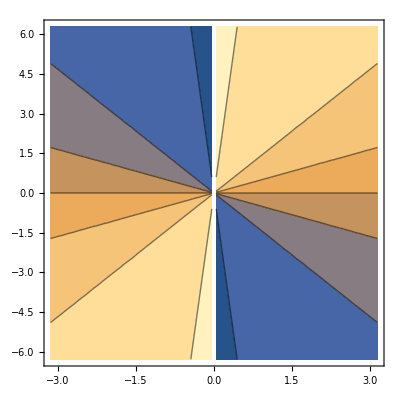

```mathematica
ContourPlot[ArcTan[y/x],{x,-Pi,Pi},{y,-2 Pi,2 Pi}]
```